# Candidate Boat Designs

### 3D Functions

```mathematica
boat1[n_] := Abs[y/n]^(1/3)<=z≤2
expBoat[n_]:=Exp[Abs[y/(n*(x^2-4))]]+(x^2-4)/6≤z≤1
expBoat2D[n_]:=Exp[Abs[y/(n*-4)]]-(2/3)≤z≤1
powBoat[pow_] := (2*Abs[y/2]^pow)+x^2/2≤z≤2 && -2 ≤ x≤ 2
cubicBoat[n_]:=((y/(n*(x^2-4)))-1)^3+x^2/2+1≤z≤2&&-((y/(n*(x^2-4)))+1)^3+1+x^2/2≤z≤2&&-1.99≤x≤1.99
points = {{-2,2},{-1,0},{0,1},{1,0},{2,2}};
polyBoat[n_]:=n*Fit[points,{1,y,y^2,y^3,y^4},y]≤z≤2&&-2≤x≤2
```

```mathematica
polyBoat[1]
```

1.-8.426×10^-16 y-1.41667 y^2+1.42535×10^-16 y^3+0.416667 y^4≤z≤2&&-2≤x≤2

```mathematica
Manipulate[RegionPlot3D[expBoat[n],{y,-2,2},{z,0,2},{x,-1.999,1.9999},Axes->True,AxesLabel->Automatic],{n,{0.4,1.5,2,2.5,3}}]
```

RegionPlot3D::boolf: expBoat[0.4] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: expBoat[0.4] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: expBoat[0.4] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: expBoat[0.4] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

```mathematica
Manipulate[RegionPlot3D[powBoat[n],{y,-2,2},{z,0,2},{x,-2,2},Axes->True,AxesLabel->Automatic],{n,{0.4,1,1.5,2,2.5,3}}]
```

RegionPlot3D::boolf: powBoat[0.4] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: powBoat[0.4] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: powBoat[0.4] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: powBoat[0.4] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: powBoat[0.4] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

```mathematica
Manipulate[RegionPlot3D[cubicBoat[n],{y,-2,2},{z,0,2},{x,-1.99,1.99},Axes->True,AxesLabel->Automatic],{n,{0.2,1,1.5,2,2.5,3}}]
```

RegionPlot3D::boolf: cubicBoat[0.2] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: cubicBoat[0.2] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: cubicBoat[0.2] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: cubicBoat[0.2] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: cubicBoat[0.2] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

```mathematica
Manipulate[RegionPlot3D[polyBoat[n],{y,-2,2},{z,0,2},{x,-1.99,1.99},Axes->True,AxesLabel->Automatic],{n,{0.2,1,1.5,2,2.5,3}}]
```

RegionPlot3D::boolf: polyBoat[1] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: polyBoat[1] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: polyBoat[1] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: polyBoat[1] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

RegionPlot3D::boolf: polyBoat[1] must be a Boolean function.

General::stop: Further output of RegionPlot3D::boolf will be suppressed during this calculation.

### Calculation of COM/COB of 3D Boats

```mathematica
mass[n_?NumberQ]:=NIntegrate[1/4,{x,y,z}∈ImplicitRegion[expBoat[n],{x,y,z}],AccuracyGoal->5]
mass2D[n_?NumberQ]:=NIntegrate[1/4,{y,z}∈ImplicitRegion[expBoat2D[n],{y,z}],AccuracyGoal->5]

comX[n_?NumberQ]:=NIntegrate[x/4,{x,y,z}∈ImplicitRegion[expBoat[n],{x,y,z}],AccuracyGoal->5]/mass[n]
comY[n_?NumberQ]:=NIntegrate[y/4,{x,y,z}∈ImplicitRegion[expBoat[n],{x,y,z}],AccuracyGoal->5]/mass[n]
comZ[n_?NumberQ]:=NIntegrate[z/4,{x,y,z}∈ImplicitRegion[expBoat[n],{x,y,z}],AccuracyGoal->5]/mass[n]
comY2D[n_?NumberQ]:=NIntegrate[y/4,{y,z}∈ImplicitRegion[expBoat2D[n],{y,z}],AccuracyGoal->5]/mass2D[n]
comZ2D[n_?NumberQ]:=NIntegrate[z/4,{y,z}∈ImplicitRegion[expBoat2D[n],{y,z}],AccuracyGoal->5]/mass2D[n]
```

```mathematica
water[theta_, b_] := If[theta==π/2,-2≤y≤0&&0≤z≤2,If[theta<π/2,z≤Tan[-theta]*y+b,z≥Tan[-theta]*y+b]]
submergedRegion[n_,theta_,b_] := expBoat[n] && water[theta,b]
submerged2D[n_,theta_,b_]:=expBoat2D[n]&&water[theta,b]
massOfWater[n_?NumberQ,theta_?NumberQ,b_?NumberQ]:=NIntegrate[1,{x,y,z}∈ImplicitRegion[submergedRegion[n,theta,b],{x,y,z}],AccuracyGoal->5]
massOfWater2D[n_?NumberQ,theta_?NumberQ,b_?NumberQ]:=NIntegrate[1,{y,z}∈ImplicitRegion[submerged2D[n,theta,b],{y,z}],AccuracyGoal->5]
findB[n_,theta_] :=FindRoot[mass[n]-massOfWater[n,theta,b]==0,{b,.5},AccuracyGoal->3]
findB2D[n_,theta_] :=FindRoot[mass2D[n]-massOfWater2D[n,theta,b]==0,{b,.5},AccuracyGoal->3]
```

```mathematica
cobX[n_?NumberQ,theta_?NumberQ]:=NIntegrate[x,{x,y,z}∈ImplicitRegion[submergedRegion[n,theta,b/.findB[n,theta]],{x,y,z}],AccuracyGoal->5]/massOfWater[n,theta,b/.findB[n,theta]]
cobY[n_?NumberQ,theta_?NumberQ]:=NIntegrate[y,{x,y,z}∈ImplicitRegion[submergedRegion[n,theta,b/.findB[n,theta]],{x,y,z}],AccuracyGoal->5]/massOfWater[n,theta,b/.findB[n,theta]]
cobZ[n_?NumberQ,theta_?NumberQ]:=NIntegrate[z,{x,y,z}∈ImplicitRegion[submergedRegion[n,theta,b/.findB[n,theta]],{x,y,z}],AccuracyGoal->5]/massOfWater[n,theta,b/.findB[n,theta]]


cobY2D[n_?NumberQ,theta_?NumberQ]:=NIntegrate[y,{y,z}∈ImplicitRegion[submerged2D[n,theta,b/.findB2D[n,theta]],{y,z}],AccuracyGoal->5]/massOfWater2D[n,theta,b/.findB2D[n,theta]]
cobZ2D[n_?NumberQ,theta_?NumberQ]:=NIntegrate[z,{y,z}∈ImplicitRegion[submerged2D[n,theta,b/.findB2D[n,theta]],{y,z}],AccuracyGoal->5]/massOfWater2D[n,theta,b/.findB2D[n,theta]]
```

```mathematica
comZ[.5]
```

0.787024

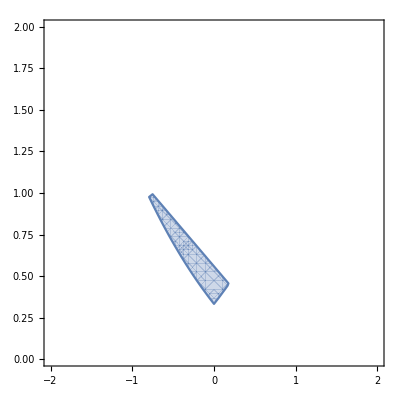

0.147767

-0.268292

```mathematica
test=submerged2D[.4,N[π/6],b/.findB2D[.4,N[π/6]]];
RegionPlot[test,{y,-2,2},{z,0,2}]
test2=massOfWater2D[.4,N[π/6],b/.findB2D[.4,N[π/6]]]
NIntegrate[y,{y,z}∈ImplicitRegion[test,{y,z}],AccuracyGoal->5]/test2
```

```mathematica
findB2D[.4,D[π/6]]
```

{b→0.558898}

```mathematica
mass2D[1]/massOfWater2D[1,N[π/6],b/.findB2D[1,D[π/6]]]
```

1.

0.558898

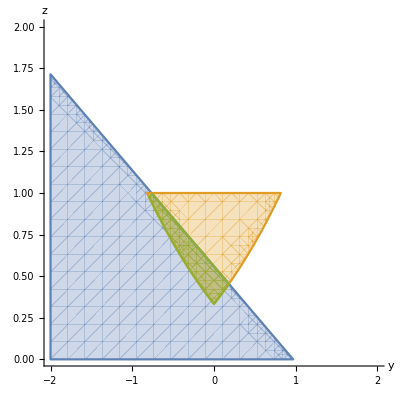

```mathematica
curB=b/.findB2D[.4,D[π/6]]
RegionPlot[{water[D[π/6],curB],expBoat2D[.4],submerged2D[.4,D[π/6],curB]},{y,-2,2},{z,0,2},Axes->True,AxesLabel->Automatic,Frame->None]
```

```mathematica
submergedRegion[1,π/6,.5]
```

ⅇ^Abs[y/(-4+x^2)]+1/6 (-4+x^2)≤z≤1&&z≤0.5-y/(√3)

```mathematica
massOfWater[1,1,.5]
```

0.756221

```mathematica
findB[1,D[π/6]]
```

{b→0.485229}

```mathematica
submergedRegion[1,π/6,b/.findB[1,π/6]]
```

ⅇ^Abs[y/(-4+x^2)]+1/6 (-4+x^2)≤z≤1&&z≤0.485229-y/(√3)

```mathematica
RegionPlot3D[ⅇ^Abs[y/(-4+x^2)]+1/6 (-4+x^2)≤z≤1&&z≤0.48522935750544505-y/(√3),{y,-2,2},{z,0,2},{x,-1.999,1.9999},Axes->True,AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Manipulate[Show[RegionPlot3D[expBoat[n],{y,-2,2},{z,0,2},{x,-1.999,1.9999},Axes->True,AxesLabel->Automatic,Mesh->None,PlotStyle->Opacity[.25]],RegionPlot3D[submergedRegion[n,D[π/6],b/.findB[n,D[π/6]]],{y,-2,2},{z,0,2},{x,-1.999,1.9999},Axes->True,AxesLabel->Automatic,Mesh->None,PlotStyle->Yellow]],{n,{0.4,1.5,2,2.5,3}}]
```

```mathematica
Show[RegionPlot3D[expBoat[1],{y,-2,2},{z,0,2},{x,-1.999,1.9999},Axes->True,AxesLabel->Automatic,Mesh->None,PlotStyle->Opacity[.25]],RegionPlot3D[submergedRegion[1,D[π/6],b/.findB[1,D[π/6]]],{y,-2,2},{z,0,
2},{x,-1.999,1.9999},Axes->True,AxesLabel->Automatic,Mesh->None,PlotStyle->Yellow]]
```

-Graphics3D-

### Calculating Moment

```mathematica
buoyForce[n_,theta_]:=mass[n]*(9.81)
buoyForce2D[n_?NumberQ,theta_?NumberQ]:=mass2D[n]*(9.81)
momentArm[n_,theta_]:={cobX[n,theta]-comX[n],cobY[n,theta]-comY[n],cobZ[n,theta]-comZ[n]}
moment[n_,theta_]:=momentArm[n,theta]×{buoyForce[n,theta]*-Sin[theta],buoyForce[n,theta]*Cos[theta],0}

momentArm2D[n_,theta_]:={0,cobY2D[n,theta]-comY2D[n],cobZ2D[n,theta]-comZ2D[n]}
moment2D[n_,theta_]:=momentArm2D[n,theta]×{0,buoyForce2D[n,theta]*-Sin[theta],buoyForce2D[n,theta]*Cos[theta]}
```

```mathematica
cobZ2D[.4,N[π/6]]

(*momentArm2D[.4,N[π/6]]
moment2D[.4,N[π/6]]*)
```

0.626649

```mathematica
comZ2D[.4]
```

0.768212

```mathematica
NIntegrate[y,{y,z}∈ImplicitRegion[submerged2D[.4,.7,b/.findB2D[.4,.7]],{y,z}],AccuracyGoal->5]/massOfWater2D[.4,.7,b/.findB2D[.4,.7]]
```

-0.351585

```mathematica
momentArm2D[.4,N[π/6]]
```

{0,-0.268292,-0.141564}

```mathematica
moment2D[.4,N[π/6]]
```

LibraryFunction::verserr: An error due to an incompatible function call was encountered evaluating the function setFacets. The library was compiled with a previous WolframLibrary version. Recompile with the current version to fix the error.

BoundaryMeshRegion::could not make representation: -- Message text not found -- (TetGenLinkMesh)

TriangulateMesh::tmfail: TriangulateMesh failed to triangulate the mesh.

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region ImplicitRegion[«2»].

NIntegrate::femtemnbb: The bounds for ImplicitRegion[ⅇ^(2.5 Abs[Times[«2»]])+1/6 (-4+x^2)≤z≤1&&x≥0&&y≥0,{x,y,z}] are {{-∞,∞},{-∞,∞},{-∞,∞}}. Unless finite numeric bounds are specified, the mesh generation will constrain the region to have finite bounds.

LibraryFunction::verserr: An error due to an incompatible function call was encountered evaluating the function setFacets. The library was compiled with a previous WolframLibrary version. Recompile with the current version to fix the error.

BoundaryMeshRegion::could not make representation: -- Message text not found -- (TetGenLinkMesh)

TriangulateMesh::tmfail: TriangulateMesh failed to triangulate the mesh.

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region ImplicitRegion[«2»].

NIntegrate::femtemnbb: The bounds for ImplicitRegion[ⅇ^(2.5 Abs[Times[«2»]])+1/6 (-4+x^2)≤z≤1&&x≥0&&y≥0,{x,y,z}] are {{-∞,∞},{-∞,∞},{-∞,∞}}. Unless finite numeric bounds are specified, the mesh generation will constrain the region to have finite bounds.

LibraryFunction::verserr: An error due to an incompatible function call was encountered evaluating the function setFacets. The library was compiled with a previous WolframLibrary version. Recompile with the current version to fix the error.

General::stop: Further output of LibraryFunction::verserr will be suppressed during this calculation.

BoundaryMeshRegion::could not make representation: -- Message text not found -- (TetGenLinkMesh)

General::stop: Further output of BoundaryMeshRegion::could not make representation will be suppressed during this calculation.

TriangulateMesh::tmfail: TriangulateMesh failed to triangulate the mesh.

General::stop: Further output of TriangulateMesh::tmfail will be suppressed during this calculation.

DiscretizeRegion::drf: DiscretizeRegion was unable to discretize the region ImplicitRegion[«2»].

General::stop: Further output of DiscretizeRegion::drf will be suppressed during this calculation.

NIntegrate::femtemnbb: The bounds for ImplicitRegion[ⅇ^(2.5 Abs[Times[«2»]])+1/6 (-4+x^2)≤z≤1&&x≥0&&y≥0,{x,y,z}] are {{-∞,∞},{-∞,∞},{-∞,∞}}. Unless finite numeric bounds are specified, the mesh generation will constrain the region to have finite bounds.

{-2.9737 NIntegrate[1/4,{x,y,z}∈ImplicitRegion[expBoat[0.4],{x,y,z}],AccuracyGoal→5],0.,0.}

### Calculating Prismatic Coefficient

```mathematica
ClearAll[sliceBoat]
curB=b/.findB[.4,0]
xMax[n_] :=FindRoot[1+((x^2-4)/6)-curB[n],{x,1}]
xLim = x/.xMax[.4]
sliceBoat[n_]:=submerged2D[n,0,curB[.4]]&&-xLim≤x≤xLim
sliceBoat[.4]
prisCoeff[n_?NumberQ]:=NIntegrate[1,{x,y,z}∈ImplicitRegion[submergedRegion[n,0,curB],{x,y,z}],AccuracyGoal->5]/NIntegrate[1,{x,y,z}∈ImplicitRegion[sliceBoat[n],{x,y,z}]]
prisCoeff[.4]
Show[RegionPlot3D[sliceBoat[.4] && -2 ≤x≤2,{x,-2,2},{y,-2,2},{z,0,2},Axes->True,AxesLabel->Automatic,Mesh->None,PlotStyle->Opacity[.25]],RegionPlot3D[expBoat[.4],{x,-1.999,1.999},{y,-2,2},{z,0,2},Axes->True,AxesLabel->Automatic,Mesh->None,PlotStyle->Yellow]]

(*Integrate[1,{x,y,z}∈ImplicitRegion[sliceBoat[.4],{x,y,z}]]
Integrate[1,{x,y,z}∈ImplicitRegion[expBoat[.4],{x,y,z}]]*)
```

```mathematica
FindMaximum[submerged2D[.4,0,b/.findB[.4,0]],{x,1}]
```

$Aborted

```mathematica
findB[.4,0]
```

{b→0.705573}

```mathematica
FindRoot[1+((x^2-4)/6)-b/.findB[.4,0],{x,1}]
```

{x→1.49447}